```mathematica
PRÀCTICA 6:SUCCESSIONS (II)
```

```mathematica
ACTIVITAT 1
```

```mathematica
En primer lloc substituirem "\"""n""\"" per "\"""n""-""1""\"" en l'equació de recurrència per tindre aïllat a[n]: 

Subscript[a, n]=1+1/(3 Subscript[a, n-1])
```

```mathematica
a[n_]=If[n==1,7,1+1/(3*a[n-1])]
```

If[n==1,7,1+1/(3 a[n-1])]

```mathematica
a[1]
```

7

```mathematica
a[2]
```

22/21

```mathematica
N[a[10],10]
```

1.263761709

```mathematica
Per "visualitzar" si la successió és convergent, podem calcular uns quants termes anb Table:
```

```mathematica
Table[N[a[n],20],{n,1,100}]
```

{7.,1.047619047619047619,1.3181818181818181818,1.2528735632183908046,1.266055045871559633,1.263285024154589372,1.2638623326959847036,1.2637418053454362078,1.2637669592976855547,1.2637617092937585517,1.263762805030398934,1.263762576336716313,1.2637626240678614264,1.2637626141057911411,1.2637626161849962632,1.2637626157510408862,1.263762615841612647,1.2637626158227092198,1.2637626158266545948,1.2637626158258311471,1.2637626158260030107,1.2637626158259671406,1.2637626158259746272,1.2637626158259730646,1.2637626158259733907,1.2637626158259733227,1.2637626158259733369,1.2637626158259733339,1.2637626158259733345,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344,1.2637626158259733344}

```mathematica
També podem representar la successió gràficament:
```

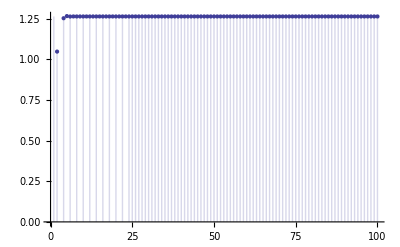

```mathematica
DiscretePlot[a[n],{n,1,100}]
```

```mathematica
Els resultats "empírics" denoten que la successió és convergent i 1.2637626158259733344 és una aproximació numèrica del seu límit
```

```mathematica
Solve[x==1+1/(3*x),x]
```

{{x→1/6 (3-√21)},{x→1/6 (3+√21)}}

```mathematica
N[%,20]
```

{{x→-0.26376261582597333443},{x→1.2637626158259733344}}

```mathematica
Comparant amb els resultats obtinguts amb Table veiem que el valor exacte del límit és 1/6 (3+√21)
```

```mathematica
ACTIVITAT 2
```

```mathematica
Substituint primer n per n-1 en la recurrència (per poder tindre aïllat Subscript[a, n] en lloc de Subscript[a, n+1]) i utilitzant If, podem definir la successió de la següent forma:
```

```mathematica
a[n_]=If[n==1,2, Sqrt[5+4*a[n-1]]]
```

If[n==1,2,√(5+4 a[n-1])]

```mathematica
a[1]
```

2

```mathematica
a[2]
```

√13

```mathematica
N[a[15],21]
```

4.99998963517891099943

```mathematica
Table[N[a[n],20],{n,1,100}]
```

{2.,3.6055512754639892931,4.407063092565836772,4.7569162668963752833,4.9018022264862442258,4.9605653816823115131,4.9842011924408956439,4.9936764782836685661,4.9974699511987737678,4.9989878780404234014,4.9995951348245883344,4.9998380513070974205,4.9999352201031954652,4.9999740879741348776,4.9999896351789109994,4.9999958540698455261,4.9999983416276631906,4.999999336651021273,4.9999997346604014687,4.999999893864159461,4.9999999575456636042,4.9999999830182654128,4.9999999932073061605,4.9999999972829224635,4.9999999989131689853,4.9999999995652675941,4.9999999998261070376,4.9999999999304428151,4.999999999972177126,4.9999999999888708504,4.9999999999955483402,4.9999999999982193361,4.9999999999992877344,4.9999999999997150938,4.9999999999998860375,4.999999999999954415,4.999999999999981766,4.9999999999999927064,4.9999999999999970826,4.999999999999998833,4.9999999999999995332,4.9999999999999998133,4.9999999999999999253,4.9999999999999999701,4.9999999999999999881,4.9999999999999999952,4.9999999999999999981,4.9999999999999999992,4.9999999999999999997,4.9999999999999999999,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.}

```mathematica
Els resultats "empírics" mostren que es tracta d'una successió convergent amb límit 5
```

```mathematica
ACTIVITAT 3
```

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[n+1]==2*a[n]+1,a[1]==1},a[n],n]
```

{{a[n]→-1+2^n}}

```mathematica
Per tant, el terme general és Subscript[a, n]=2^n- 1
```

```mathematica
ACTIVITAT 4
```

```mathematica
Canviant prèviament n per n-1 en la recurrència per a tindre Subscript[a, n] aïllada:
```

```mathematica
a[n_]=If[n==2,-3,a[n-1]/5+(n-1)^2-1]
```

If[n==2,-3,1/5 a[n-1]+(n-1)^2-1]

```mathematica
N[a[12]]
```

143.594

```mathematica
N[a[100]]
```

12188.6

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[2]==-3, a[n+1]==a[n]/5+n^2-1},a[n],n]
```

{{a[n]→1/32 5^(1-n) (-455+7 5^n-4 5^(1+n) n+8 5^n n^2)}}

```mathematica
Per tant, l'expressió explícita del terme general de la successió és Subscript[a, n]=1/32 5^(1-n) (-455+7 5^n-4 5^(1+n) n+8 5^n n^2)
```

```mathematica
ACTIVITAT 5
```

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[1]==1,a[2]==1,a[n+2]==a[n]+a[n+1]},a[n],n]
```

{{a[n]→Fibonacci[n]}}

```mathematica
Veiem que Mathematica té ja predefinida la funció Fibonacci[n] que dóna, per a cada valor de n, el n-éssim nombre de Fibonacci. I és el que retorna quan apliquem RSolve a la recurrència (no ens mostra l'expressió explícita de Fibonacci[n]). Si volem aquesta epressió necessitarem resoldre la recurrència "\"""a"" ""mà""\"" (encara que podem contar amb l'ajuda de Mathematica per als càlculs):
```

```mathematica
L'equació característica és x^2-x-1=0. Si la resolem tenim:
```

```mathematica
Solve[x^2-x-1==0,x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
Per tant, la solució general de la recurrència és:
Subscript[a, n]=C1(1/2 (1-√5))^n + C2(1/2 (1+√5))^n

Tenint en compte les condicions inicials, obtenim el sistema:
C1(1/2 (1-√5)) + C2(1/2 (1+√5))=1; 
C1(1/2 (1-√5))^2 + C2(1/2 (1+√5))^2=1

El resolem:
```

```mathematica
Solve[{C1*1/2(1-√5)+ C2*1/2 (1+√5)==1,C1*(1/2 (1-√5))^2 + C2*(1/2 (1+√5))^2==1},{C1,C2}]
```

{{C1→-((-1+√5) (1+√5))/(4 √5),C2→-(-5-√5)/(5 (1+√5))}}

```mathematica
Ara substituïm els valors de les constants en la solució general:
```

```mathematica
C1(1/2 (1-√5))^n + C2(1/2 (1+√5))^n/.%
```

{-(2^(-2-n) (1-√5)^n (-1+√5) (1+√5))/(√5)-1/5 2^-n (-5-√5) (1+√5)^(-1+n)}

```mathematica
Simplify[%]
```

{-(2^-n (5+√5) ((1-√5)^n-(1+√5)^n))/(5 (1+√5))}

```mathematica
Si volem, podem comprovar que realment es tracta del terme general de la sucessió de Fibonacci:
```

```mathematica
a[n_]=-(2^-n (5+√5) ((1-√5)^n-(1+√5)^n))/(5 (1+√5))
```

-(2^-n (5+√5) ((1-√5)^n-(1+√5)^n))/(5 (1+√5))

```mathematica
a[1]
```

(5+√5)/(√5 (1+√5))

```mathematica
Simplify[%]
```

1

```mathematica
a[2]
```

-((5+√5) ((1-√5)^2-(1+√5)^2))/(20 (1+√5))

```mathematica
Simplify[%]
```

1

```mathematica
Simplify[a[3]]
```

2

```mathematica
Simplify[a[4]]
```

3

```mathematica
Table[Simplify[a[n]],{n,1,15}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610}

```mathematica
ACTIVITAT 6
```

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[n+2]==6*a[n+1]-9*a[n]+5*n, a[0]==3, a[1]==-2},a[n],n]
```

{{a[n]→1/4 (5+7 3^n+5 n-13 3^n n)}}

```mathematica
El terme general és Subscript[a, n]=1/4(5+7*3^n+5*n-13*3^n*n)
```

```mathematica
ACTIVITAT 7
```

```mathematica
RSolve[a[n+3]-3*a[n+2]-a[n+1]+3*a[n]==2^n,a[n],n]
```

{{a[n]→-2^n/3+(-1)^n C[1]+C[2]+3^n C[3]}}

```mathematica
La solució general és, per tant, la successió que té com a terme general

Subscript[a, n]=C_1*(-1)^n + C_2 + C_3*3^n - 2^n/3 

sent C1 i C2 constants.
```